```mathematica
h:=1/2(k11 Jx^(3/2) Sqrt[Jy]+k12 Sqrt[Jx] Jy^(3/2))(Cos[ϕx-ϕy+2(δ s)/R+α])+3/8(p Jx^2+r Jy^2+2 q Jx Jy)-3/4f2 Jx Jy (Cos[2ϕx-2ϕy+4(δ s)/R])
ϕxstr=D[h,Jx];
Jxstr=-D[h,ϕx];
ϕystr=D[h,Jy];
Jystr=-D[h,ϕy];
Jxstrd=Jxstr/.{Jx->a Jx[t],Jy->a Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
Jystrd=Jystr/.{Jx->a Jx[t],Jy->a Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕxstrd=ϕxstr/.{Jx->a Jx[t],Jy->a Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕystrd=ϕystr/.{Jx->a Jx[t],Jy->a Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
```

```mathematica
inputpr=({Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==Jxv,Jy[0]==Jyv,ϕx[0]==ϕxv,ϕy[0]==ϕyv}/.{f2->f2,R->1/π,p->p,q->q,r->r,δ->δ,s->t,a->a,α->α,k11->k11,k12->k12});
```

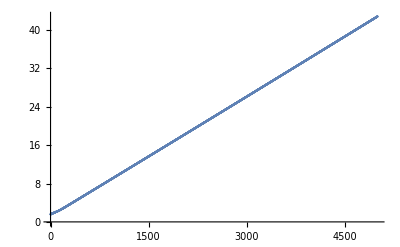

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δ->0.001,f2->10,p->10,q->10,r->10,k11->10,k12->10,a->0.001,α->1};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.95},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]];
ListPlot[Table[{t1,(ϕx[t]/.locsol)/.{t->t1}},{t1,0,5000,1}]]
```

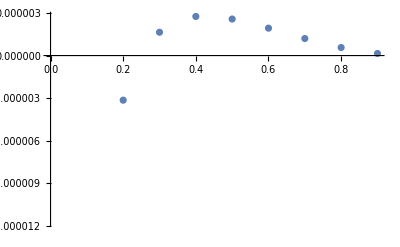
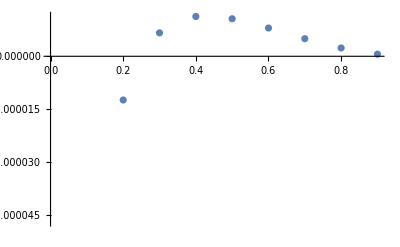
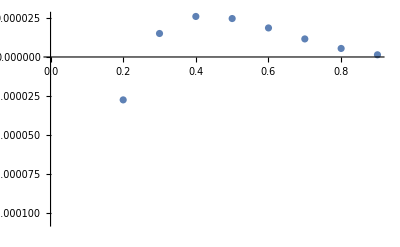
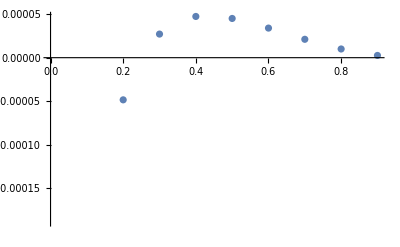
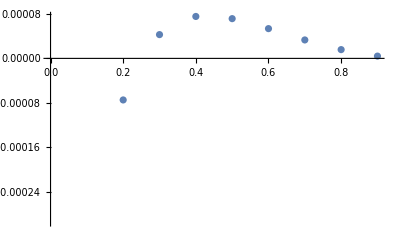
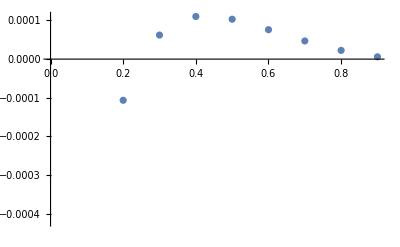
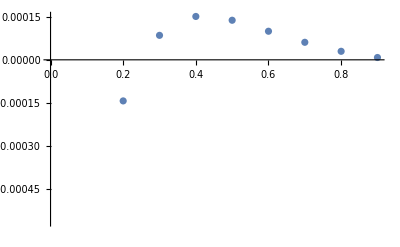
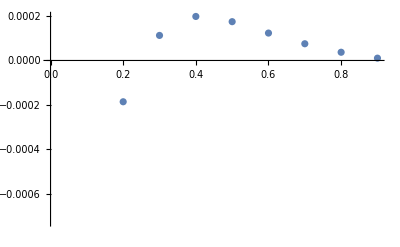

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δ->.001,f2->0,p->0,q->0,r->0,k11->0,k12->100,a->a,α->1};
Table[ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->t1})],{t1,0,5000,500}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.1,0.9,.1}]],{a,0.00001,0.0001,0.00001}]
```

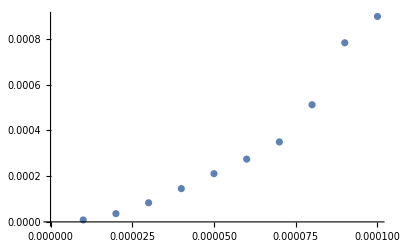

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δ->.001,f2->0,p->0,q->0,r->0,k11->100,k12->0,a->a,α->1};
ListPlot[Table[{a,Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.1,0.9,.1}]]},{a,0.00001,0.0001,0.00001}]]
```

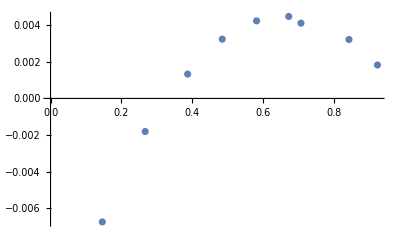

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.1,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->t1})],{t1,0,5000,500}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.1,0.9,.1}]]
```

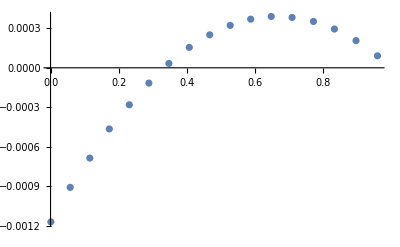

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.3,f2v->-.05,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
cplot=ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->t1})],{t1,0,5000,500}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.001,0.999,.06}]]
```

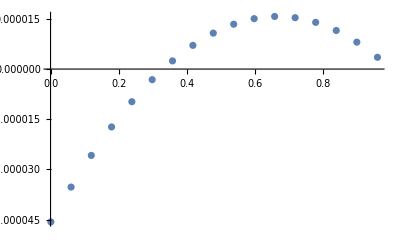

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.3,f2v->-.01,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
c1plot=ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->t1})],{t1,0,5000,500}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.001,0.999,.06}]]
```

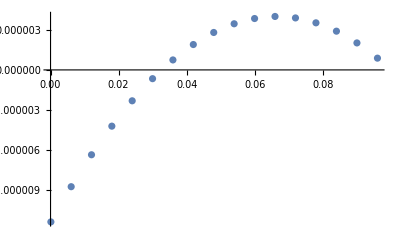

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.3,f2v->-.05,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
c2plot=ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->t1})],{t1,0,5000,500}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.0001,0.0999,.006}]]
```

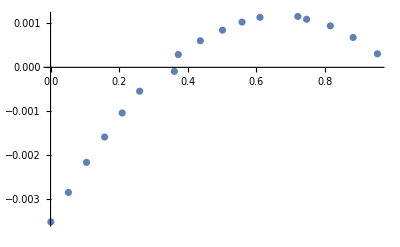

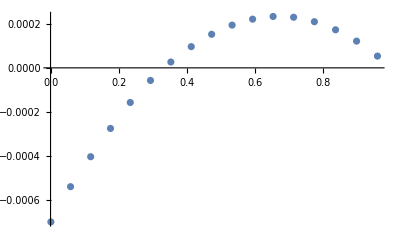

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->-.05,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
c3plot=ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->t1})],{t1,0,5000,500}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.001,0.999,.06}]]
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.5,f2v->-.05,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
c4plot=ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->t1})],{t1,0,5000,500}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.001,0.999,.06}]]
```

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->II-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.1,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.01,0.09,.01}]]
Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.2},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.2},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.02,0.18,.02}]]
Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.3},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.3},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.03,0.27,.03}]]
Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.4},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.4},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.04,0.36,.04}]]
Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.5},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc/.{II->.5},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.05,0.45,.05}]]
```

0.0000469691

0.000183112

0.00041696

0.000732703

0.00115699

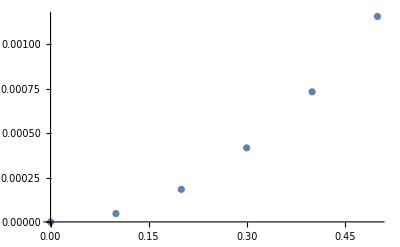

```mathematica
aplot=ListPlot[{{0,0},{.1,0.0000469691210346479},{.2,0.00018311155137783235},{.3,0.0004169596507615248},{.4,0.00073270347381369},{.5,0.0011569928431083203}}]
```

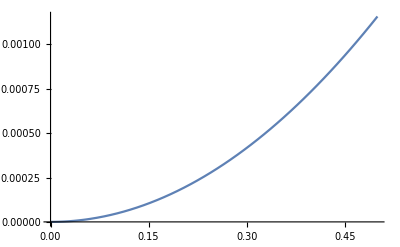

```mathematica
bplot=Plot[0.00463x^2,{x,0,0.5}]
```

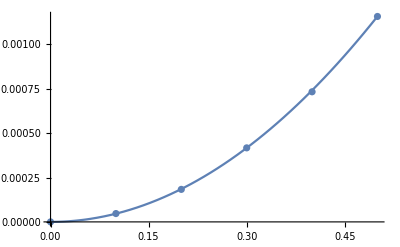

```mathematica
Show[{aplot,bplot}]
```

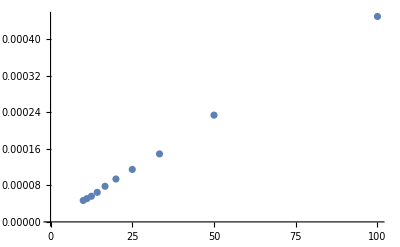

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->δv,f2v->.01,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
ListPlot[Table[{1/δv,Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.1,0.9,.1}]]},{δv,0.01,.1,0.01}]]
```

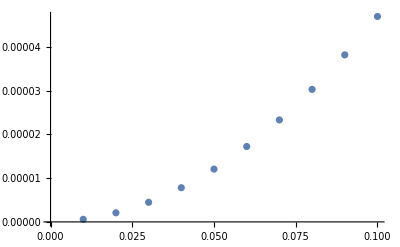

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,δv->.1,f2v->f2v,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
f2plot=ListPlot[Table[{f2v,Max[Table[(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000,{Jxv1,0.01,0.09,.01}]]},{f2v,0.01,0.1,0.01}]]
```

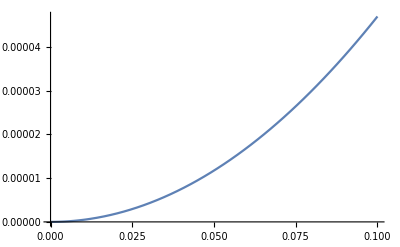

```mathematica
bf2plot=Plot[0.0047x^2,{x,0,0.1}]
```

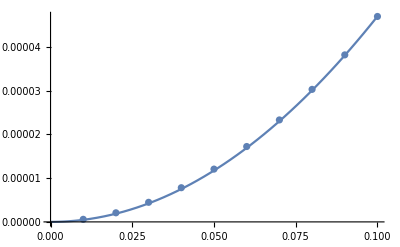

```mathematica
Show[{f2plot,bf2plot}]
```

```mathematica
8.2 0.0463
```

0.37966

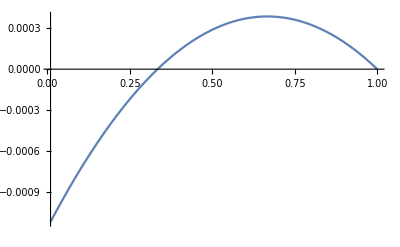

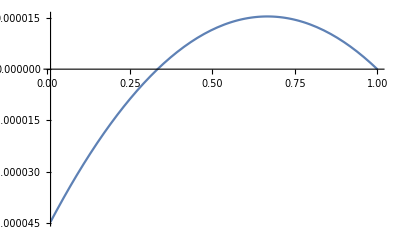

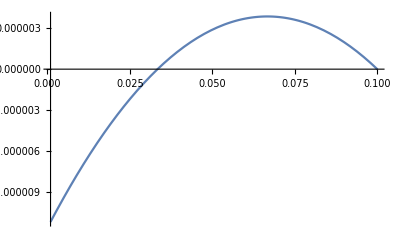

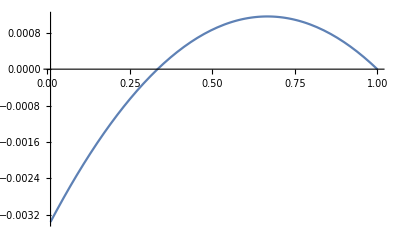

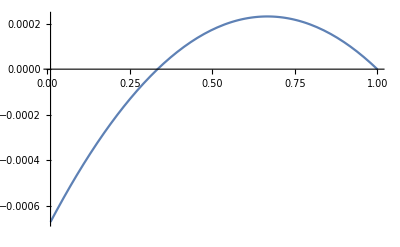

```mathematica
dplot=Plot[0.0463 1 0.0025/0.3 (-8.2(2.1x-1.4)^2+4)0.25,{x,0.01,1}]
d1plot=Plot[0.0463 1 0.0001/0.3 (-8.2(2.1x-1.4)^2+4)0.25,{x,0.01,1}]
d2plot=Plot[0.0463 1 0.0025/0.3 (-8.2(2.1x-.14)^2+4 0.01)0.25,{x,0.001,.1}]
d3plot=Plot[0.0463 1 0.0025/0.1 (-8.2(2.1x-1.4)^2+4)0.25,{x,0.01,1}]
d4plot=Plot[0.0463 1 0.0025/0.5 (-8.2(2.1x-1.4)^2+4)0.25,{x,0.01,1}]
```

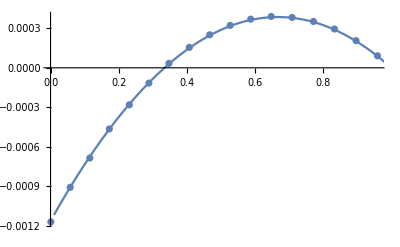

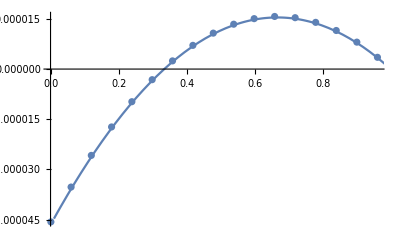

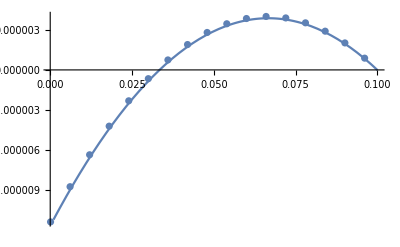

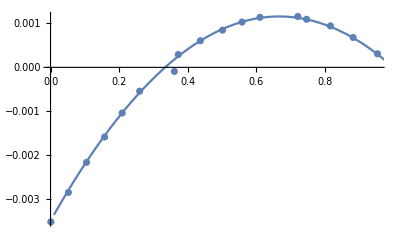

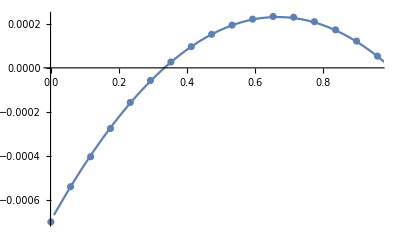

```mathematica
Show[{cplot,dplot}]
Show[{c1plot,d1plot}]
Show[{c2plot,d2plot},PlotRange->All]
Show[{c3plot,d3plot}]
Show[{c4plot,d4plot}]
```

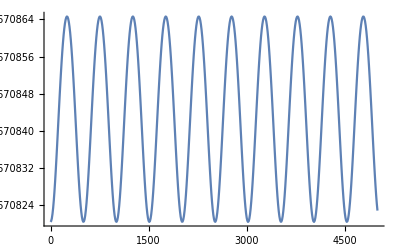

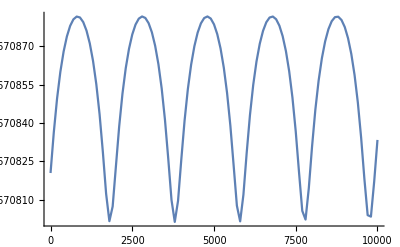

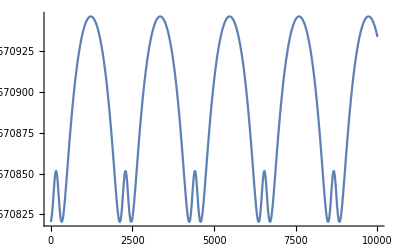

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δ->.001,f2->100,p->0,q->0,r->0,k11->0,k12->-0,a->0.0001,α->0};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.45},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]];
ListPlot[Table[{t1,(Sqrt[Jx[t]/.locsol])/.{t->t1}},{t1,0,5000,10}],Joined->True]
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δ->.001,f2->0,p->0,q->0,r->0,k11->200,k12->-0,a->0.0001,α->0};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.45},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]];
ListPlot[Table[{t1,(Sqrt[Jx[t]/.locsol])/.{t->t1}},{t1,0,10000,100}],Joined->True]
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δ->.001,f2->100,p->0,q->0,r->0,k11->-100,k12->100,a->0.0001,α->0};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.45},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]];
ListPlot[Table[{t1,(Sqrt[Jx[t]/.locsol])/.{t->t1}},{t1,0,10000,10}],Joined->True]
```

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δ->.001,f2->k11,p->0,q->0,r->0,k11->k11,k12->0,a->0.0001,α->0};
sred=Table[Mean[Table[(Sqrt[Jx[t]/.Flatten[NDSolve[inloc/.{Jxv1->.45},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,10000}]]])/.{t->t1},{t1,0,10000,100}]],{k11,-100,100,33.33}];
```

```mathematica
soltable=Table[Flatten[NDSolve[inloc/.{Jxv1->.45,k11->-100+33.3 (j-1)},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,10000}]],{j,1,7}];
```

```mathematica
x=Table[Table[(Sin[t1 π/10000])^2(((Sqrt[Jx[t]/.soltable[[j]]])/.{t->t1})-sred[[j]]),{t1,0,10000}],{j,1,7}];
```

```mathematica
listfourierx=Table[Abs[Fourier[x[[i,All]]]],{i,1,7}];
```

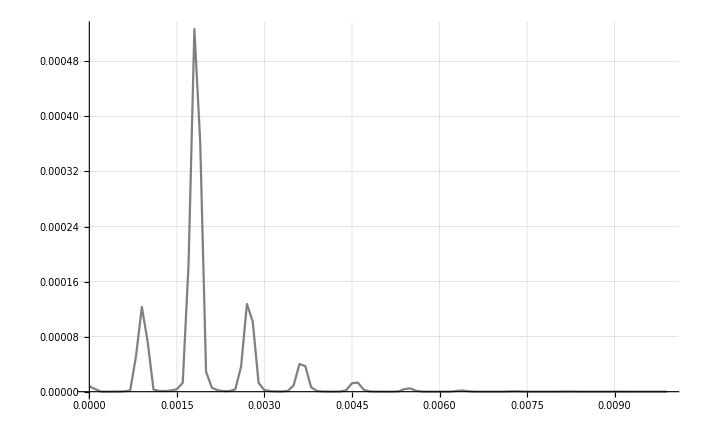
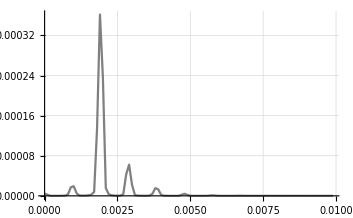
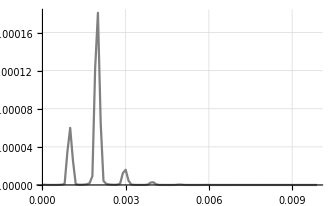
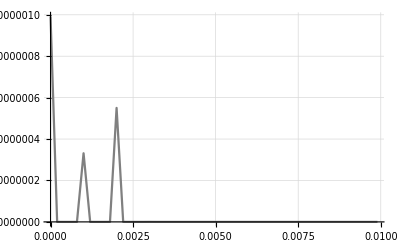
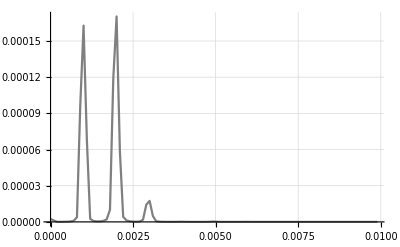
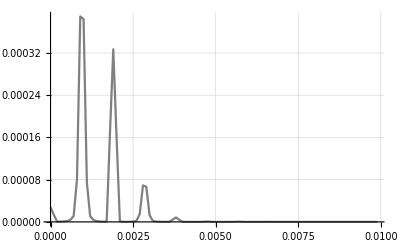
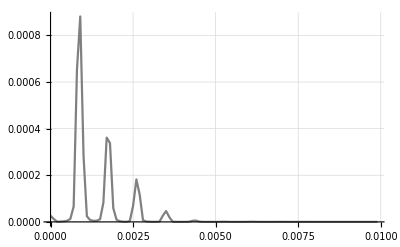

```mathematica
Table[ListPlot[Table[{(n1-1)/(10000),listfourierx[[k,n1]]},{n1,1,10001}][[Range[0,100]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic],{k,1,7}]
```

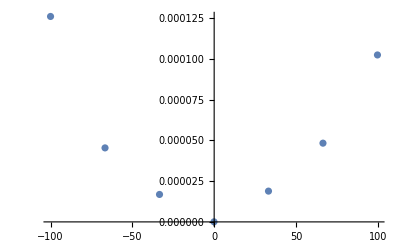

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δ->.001,f2->-k11,p->0,q->0,r->0,k11->k11,k12->-k11,a->0.0001,α->0};
ListPlot[Table[{k11,Max[Table[(Sqrt[Jx[t]/.Flatten[NDSolve[inloc/.{Jxv1->.45},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,10000}]]])/.{t->t1},{t1,0,10000,100}]]-Min[Table[(Sqrt[Jx[t]/.Flatten[NDSolve[inloc/.{Jxv1->.45},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,10000}]]])/.{t->t1},{t1,0,10000,100}]]},{k11,-100,100,33.3}]]
```

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δ->.001,f2->-0,p->0,q->0,r->0,k11->k11,k12->-0,a->0.0001,α->0};
Table[ListPlot[Abs[Fourier[Table[(Sin[t1 π/10000])^2 (Sqrt[Jx[t]/.Flatten[NDSolve[inloc/.{Jxv1->.45},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,10000}]]])/.{t->t1},{t1,0,10000}]]][[Range[10,200]]],Joined->True],{k11,100,100,33.3}]
```

$Aborted

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δ->.001,f2->100,p->0,q->0,r->0,k11->par,k12->0,a->0.0001,α->0};
Manipulate[ListPlot[Table[{t1,(Sqrt[Jx[t]/.Flatten[NDSolve[inloc/.{Jxv1->.45,par->par1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]]])/.{t->t1}},{t1,0,5000,100}],Joined->True],{par1,-100,100}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==-1.5×10^-8 k11 Jx[t] Jy[t] Sin[Plus[«3»]]+1/2 (0.+Times[«4»]) Sin[Plus[«3»]],Jy'[t]==1.5×10^-8 k11 Jx[t] Jy[t] Sin[Plus[«3»]]-1/2 (0.+Times[«4»]) Sin[Plus[«3»]],ϕx'[t]==0.+1/2 Cos[Plus[«3»]] (0.+Times[«4»])-0.000075 k11 Cos[Plus[«3»]] Jy[t],ϕy'[t]==0.-0.000075 k11 Cos[Plus[«3»]] Jx[t]+1/2 Cos[Plus[«3»]] (0.+Times[«4»]),Jx[0]==0.45,Jy[0]==0.55,ϕx[0]==π/2,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[0]==-1.5×10^-8 k11 Jx[0] Jy[0] Sin[Plus[«3»]]+1/2 (0.+Times[«4»]) Sin[Plus[«3»]],Jy'[0]==1.5×10^-8 k11 Jx[0] Jy[0] Sin[Plus[«3»]]-1/2 (0.+Times[«4»]) Sin[Plus[«3»]],ϕx'[0]==0.+1/2 Cos[Plus[«3»]] (0.+Times[«4»])-0.000075 k11 Cos[Plus[«3»]] Jy[0],ϕy'[0]==0.-0.000075 k11 Cos[Plus[«3»]] Jx[0]+1/2 Cos[Plus[«3»]] (0.+Times[«4»]),Jx[0]==0.45,Jy[0]==0.55,ϕx[0]==π/2,ϕy[0]==0},{Jx[0],ϕx[0],Jy[0],ϕy[0]},{0,0,5000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==-1.5×10^-8 k11 Jx[t] Jy[t] Sin[Plus[«3»]]+1/2 (0.+Times[«4»]) Sin[Plus[«3»]],Jy'[t]==1.5×10^-8 k11 Jx[t] Jy[t] Sin[Plus[«3»]]-1/2 (0.+Times[«4»]) Sin[Plus[«3»]],ϕx'[t]==0.+1/2 Cos[Plus[«3»]] (0.+Times[«4»])-0.000075 k11 Cos[Plus[«3»]] Jy[t],ϕy'[t]==0.-0.000075 k11 Cos[Plus[«3»]] Jx[t]+1/2 Cos[Plus[«3»]] (0.+Times[«4»]),Jx[0]==0.45,Jy[0]==0.55,ϕx[0]==π/2,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 100 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 200 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of inloc in the first argument inloc.

ReplaceAll::reps: {NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[inloc,{Jx[0],ϕx[0],Jy[0],ϕy[0]},{0,0,5000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of inloc in the first argument inloc.

ReplaceAll::reps: {NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 100 cannot be used as a variable.

NDSolve::deqn: Equation or list of equations expected instead of inloc in the first argument inloc.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

NDSolve::dsvar: 200 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

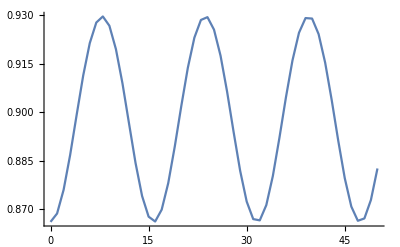

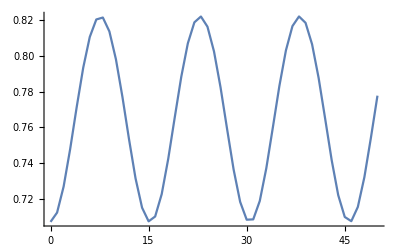

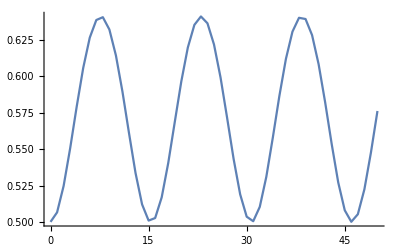

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.1,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.75},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]];
ListPlot[Table[{t1,(Sqrt[Jx[t]/.locsol])/.{t->t1}},{t1,0,50,1}],Joined->True]
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.1,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.5},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]];
ListPlot[Table[{t1,(Sqrt[Jx[t]/.locsol])/.{t->t1}},{t1,0,50,1}],Joined->True]
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.1,pv->.0,rv->0,f1v->0,k11->0,k12->0,f11->0,f21->0,q->0};
locsol=Flatten[NDSolve[inloc/.{Jxv1->.25},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]];
ListPlot[Table[{t1,(Sqrt[Jx[t]/.locsol])/.{t->t1}},{t1,0,50,1}],Joined->True]
```

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.1,pv->.0001,rv->.0001,f1v->0,k11->.00001,k12->.0001,f11->.0001,f21->.0001,q->.0001};
Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],{1,x},x]
```

-0.00407669+0.0101489 x

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.5-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.01,pv->.0,rv->.1,f1v->0,k11->.05,k12->-.05};
Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.4,.05}],{1,x},x]
```

-0.00745662+0.0148423 x

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.3-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.01,pv->.0,rv->.1,f1v->0,k11->.05,k12->-.05};
Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.05,0.25,.025}],{1,x},x]
```

-0.00449395+0.0149731 x

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.01,pv->.0,rv->.1,f1v->0,k11->.05,k12->-.05};
Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.01,0.09,.01}],{1,x},x]
```

-0.00150189+0.015031 x

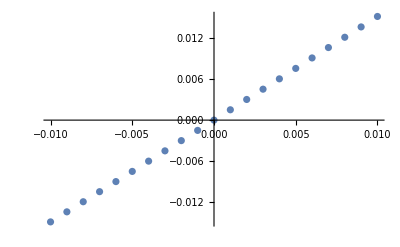

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->.1,f2v->f2v,pv->0,rv->0,k11->0,k12->0};
ListPlot[Table[{f2v,(1/x Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],{1,x},x])/.{x->10000}},{f2v,-.01,.01,0.001}]]
```

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0,pv->f2v,rv->0,k11->0,k12->0};
Fit[Table[{f2v,(1/x Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],{1,x},x])/.{x->10000}},{f2v,-1,1,0.1}],{1,x},x]
```

2.85807×10^-17+0.75 x

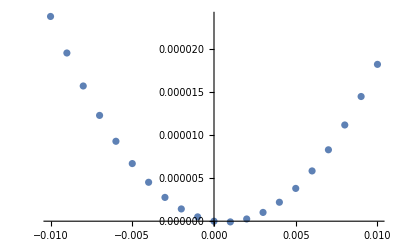

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->.1,f2v->0,pv->0,rv->0,k11->0,k12->f2v};
ListPlot[Table[{f2v,(Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],{1,x},x])/.{x->0}},{f2v,-.01,.01,0.001}]]
```

{Jx'[t]==0.000075 Jx[t] Jy[t] (0.0002 Cos[0.4 t+2 ϕx[t]-2 ϕy[t]]-2 Sin[0.4 t+2 ϕx[t]-2 ϕy[t]])-1/2 (1/2 p Jx[t]^3 √Jy[t]+0.00005 √Jx[t] Jy[t]^3) (0.0001 Cos[0.2 t+ϕx[t]-ϕy[t]]-Sin[0.2 t+ϕx[t]-ϕy[t]]),Jy'[t]==0.000075 Jx[t] Jy[t] (-0.0002 Cos[0.4 t+2 ϕx[t]-2 ϕy[t]]+2 Sin[0.4 t+2 ϕx[t]-2 ϕy[t]])-1/2 (1/2 p Jx[t]^3 √Jy[t]+0.00005 √Jx[t] Jy[t]^3) (-0.0001 Cos[0.2 t+ϕx[t]-ϕy[t]]+Sin[0.2 t+ϕx[t]-ϕy[t]]),ϕx'[t]==3/8 (0.0002 Jx[t]+0.0002 Jy[t])-0.000075 Jy[t] (Cos[0.4 t+2 ϕx[t]-2 ϕy[t]]+0.0001 Sin[0.4 t+2 ϕx[t]-2 ϕy[t]])+1/2 (3/2 p Jx[t]^2 √Jy[t]+(0.000025 Jy[t]^3)/(√Jx[t])) (Cos[0.2 t+ϕx[t]-ϕy[t]]+0.0001 Sin[0.2 t+ϕx[t]-ϕy[t]]),ϕy'[t]==3/8 (0.0002 Jx[t]+0.0002 Jy[t])-0.000075 Jx[t] (Cos[0.4 t+2 ϕx[t]-2 ϕy[t]]+0.0001 Sin[0.4 t+2 ϕx[t]-2 ϕy[t]])+1/2 ((p Jx[t]^3)/(4 √Jy[t])+0.00015 √Jx[t] Jy[t]^2) (Cos[0.2 t+ϕx[t]-ϕy[t]]+0.0001 Sin[0.2 t+ϕx[t]-ϕy[t]]),Jx[0]==Jxv1,Jy[0]==0.1-Jxv1,ϕx[0]==π/2,ϕy[0]==0}

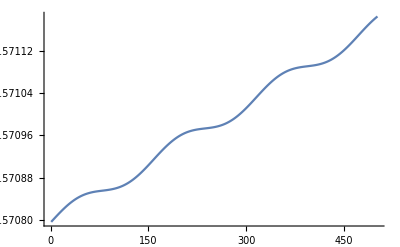
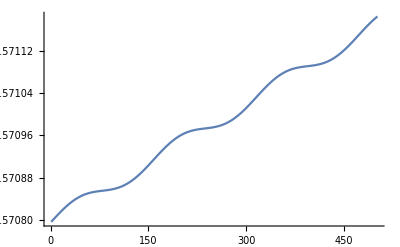
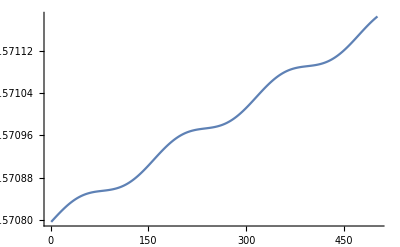
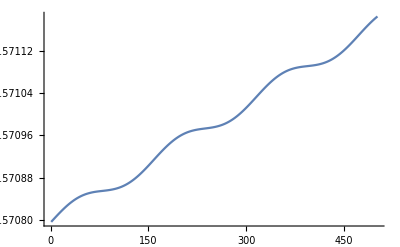
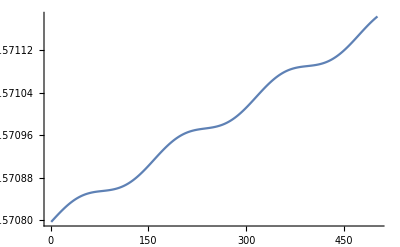

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->.1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->.0001,pv->.0001,rv->.0001,f1v->0,k11->p,k12->.0001,f11->.0001,f21->.0001,q->.0001}
Table[ListPlot[Table[ϕx[t]/.Flatten[NDSolve[inloc/.{p->p,Jxv1->0.02},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]]/.{t->t1},{t1,0,50,.1}],Joined->True],{p,-.001,.001,0.0005}]
```

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0.01,pv->.2,rv->.1,f1v->0,k11->.05,k12->-.05};
Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}]
```